## Steps for city generation

1. Start with a random base using a noise randomizer
	a. need to decide structure
	b. possible choices: tiling with each tile representing a different thing, polygons(nodes from that one article) 
2. From the base, generate more of the city
	a. Again we can use the nodes article where we can classify areas
	b. We can use wave function collapse: https://community.wolfram.com/groups/-/m/t/2435403
		wave function collapse is supposed to be easily compatible due to allowing support constraints so try my best to do that
* if we have extra time, add an option to be able to manually choose which base structure we start with.

possible tiles:
- street
- road
- building

### Perlin noise function(generating base city)

```mathematica
(*tileTypes = Association;*)
permutation = RandomSample[Range[1, 255]]; 
p = Join[permutation, permutation]; (*repeat it to avoid overflow*)
repeat = 255;

fade[t_] := t*t*t*(t*(t*6-15)+10); (* THE FADE FUNCTION >:) *)
inc[n_] := Module[{num = n+1}, If[repeat >0, num = Mod[num, repeat]]];

grad[hash_, x_, y_, z_] := Module[{hashy = Min[hash,15 ]}, 
Which[
hashy==0, x+y,
hashy==1, -x+y,
hashy==2, x-y,
hashy==3, -x-y,
hashy==4, x+z,
hashy==5, -x+z,
hashy==6, x-z,
hashy==7, -x-z,
hashy==8, y+z,
hashy==9, -y+z,
hashy==10, y-z,
hashy==11,-y-z,
hashy==12,y+x,
hashy==13,-y+z,
hashy==14,y-x,
hashy==15,-y-z]];
lerp[a_,b_,x_] :=a+x*(b-a);

perlin[a_, b_, c_] := Module[{xi = Min[Floor[a], 255], yi = Min[Floor[b], 255], zi = Min[Floor[c], 255], aaa, aba, aab, abb, baa, bba, bab, bbb, x1, x2, y1, y2, x=a, y=b, z=c, xf, yf, zf, u, v, w},If[repeat> 0,{ x = Mod[a, repeat], y = Mod[b, repeat], z = Mod[c, repeat]}];  
xf = x-Floor[x];yf = y-Floor[y];zf = z-Floor[z]; 
u = fade[xf]; v = fade[yf]; w = fade[zf];
aaa = p[[p[[p[[xi]]+yi]]+zi]]; aba = p[[p[[p[[xi]]+inc[yi]]]+zi]]; aab=p[[p[[p[[xi]]+yi]]+inc[zi]]]; abb=p[[p[[p[[xi]]+inc[yi]]]+inc[zi]]]; baa=p[[p[[p[[inc[xi]]]+yi]]+zi]]; bba=p[[p[[p[[inc[xi]]]+inc[yi]]]+zi]]; bab=p[[p[[p[[inc[xi]]]+yi]]+inc[zi]]]; bbb=p[[p[[p[[inc[xi]]]+inc[yi]]]+inc[zi]]];
x1 = lerp[grad[aaa,xf,yf,zf],grad[baa,xf-1,yf,zf], u];
x2 = lerp[grad[aba, xf, yf-1, zf], grad[bba, xf-1, yf-1, zf],u];
y1 = lerp[x1, x2, v];
x1 = lerp[grad[aab, xf, yf, zf-1], grad[bab, xf-1, yf, zf-1], u];
x2 = lerp[grad[abb, xf, yf-1, zf-1], grad[abb, xf, yf-1, zf-1], u];
y2 = lerp[x1, x2, v];
lerp[y1, y2, w]+1/2];
perlin[RandomReal[{0, 255}], RandomReal[{0, 255}], RandomReal[{0, 255}]]
```

0.605339

```mathematica
ClearAll[perlin]
```

```mathematica
perlin[a_, b_, c_] := Module[{xi = Min[Floor[a], 255], yi = Min[Floor[b], 255], zi = Min[Floor[c], 255], aaa, aba, aab, abb, baa, bba, bab, bbb, x1, x2, y1, y2, x=a, y=b, z=c, xf, yf, zf, u, v, w},If[repeat> 0,{ x = Mod[a, repeat], y = Mod[b, repeat], z = Mod[c, repeat]}];
xf = x-Floor[x];
yf = y-Floor[y];
zf = z-Floor[z];
u = fade[xf]; v = fade[yf]; w = fade[zf]; 
aaa = p[[p[[p[[xi]]+yi]]+zi]];
x]
```

```mathematica
perlin[1,2,3]
```

1

```mathematica
Clear[x,y,z]
```

```mathematica
y
```

Mod[Mod[Mod[TerminatedEvaluation[RecursionLimit],repeat],255],255]

```mathematica
y
```

Mod[Mod[Mod[TerminatedEvaluation[RecursionLimit],repeat],255],255]

```mathematica
Mod[y,repeat]
```

Mod[Mod[Mod[Mod[TerminatedEvaluation[RecursionLimit],repeat],255],255],255]

```mathematica
If[repeat> 0,{x1=Mod[x, repeat];y1=Mod[y,repeat],z1=Mod[z, repeat]}]
```

{Mod[y,255],Mod[z,255]}

# General generation structure(scrapped)

1. import city data(streets and other entities, osm)
2. use skeleton data of the streets to generate more streets(fake realistic city generation, streets/roads/ways)
3. Classify areas of existing real city using info of existing entities and algorithm https://zero.re/worldsmith/blockassign/)
4. Classify newly generated areas of fake cities: https://zero.re/worldsmith/blockassign/
5. generate entities(e.g. buildings) in the fake generated cities

```mathematica
(*New York City Times Square OSM Import *)
osm=ResourceFunction["OSMImport"][GeoBoundsRegion[{{40.755905,40.769988},{-73.994486,-73.968818}}]]
(*choose tile size and define a grid*)
bounds={{40.755905,40.769988},{-73.994486,-73.968818}};
tileSize=0.001;  (*degrees~111m lat,85m lon near NYC*)
latitudes=Range[bounds[[1,1]],bounds[[1,2]],tileSize];
longitudes=Range[bounds[[2,1]],bounds[[2,2]],tileSize];

tiles=Flatten[Table[GeoBoundingBox[GeoPosition[{lat+tileSize/2,lon+tileSize/2}],Quantity[tileSize*111000/2,"Meters"]],{lat,Most[latitudes]},{lon,Most[longitudes]}],1]
(*Assign OSM features to Tiles*)
```

## New York City Times Square(import and skeleton visualization of Street)

```mathematica
MeshRegion
```

```mathematica
osmNewYork=ResourceFunction["OSMImport"][GeoBoundsRegion[{{40.755905,40.769988},{-73.994486,-73.968818}}]];
```

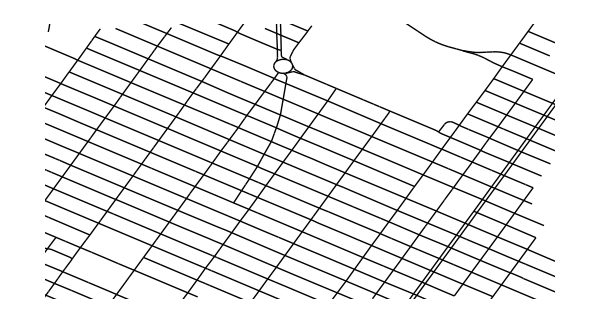

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
GeoGraphics[Values[Line[Values[osmNewYork[["Nodes",#Nodes,"Position"]]]]&/@Select[osmNewYork["Ways"],MatchQ[#[["Tags","highway"]],"residential"|"primary"|"secondary"|"tertiary"|"motorway"|"trunk"]&]]];

generateLines[openStreetMapData_]:=Values[Line[Values[openStreetMapData[["Nodes",#Nodes,"Position"]]]]&/@Select[openStreetMapData["Ways"],MatchQ[#[["Tags","highway"]],"residential"|"primary"|"secondary"|"tertiary"|"motorway"|"trunk"]&]]/.
GeoPosition[{a_,b_}]:>{b,a}

Graphics[generateLines[osmNewYork]/. GeoPosition[{lat_,lon_}]:>{lon,lat},PlotRange->{{-73.994,-73.968},{40.756,40.770}},(*your region bounds*)ImageSize->600] (*cropped*)


ImagePartition[Graphics[generateLines[osmNewYork]/. GeoPosition[{lat_,lon_}]:>{lon,lat},PlotRange->{{-73.994,-73.968},{40.756,40.770}},(*your region bounds*)ImageSize->600]
, 75]
```

```mathematica
GeoGraphics[{Values[Line[Values[osmNewYork[["Nodes",#Nodes,"Position"]]]]&/@osmNewYork["Ways"]],GeoMarker[#["Position"]]&/@osmNewYork["Nodes"]}]
```

#### Applying the algorithm to the above data

```mathematica
(*1. Only closed highway ways*)closedWays=Select[osmNewYork["Ways"],Function[w,MatchQ[w["Tags","highway"],"residential"|"primary"|"secondary"|"tertiary"|"unclassified"]&&First[w["Nodes"]]===Last[w["Nodes"]]]]


polygons=Polygon[osmNewYork["Nodes",#["Nodes"],"Position"]]&/@closedWays;

nodes=osm["Nodes"];  (*This is already an Association*)

blockPolygons=Select[Table[Module[{nodeIDs,coords},nodeIDs=way["Nodes"];
If[AllTrue[nodeIDs,KeyExistsQ[nodes,#]&],coords=nodes[#]["Position"]&/@nodeIDs;
If[Length[coords]>=3,Polygon[coords],Nothing],Nothing]],{way,closedWays}],RegionQ]
```

<||>

{}

### Markov’s Chain

```mathematica
Check discord
```